```mathematica
SetDirectory["~/code/rule146"]
```

/Users/rule146/code/rule146

```mathematica
<<Rule146`
```

```mathematica
Length@ParticleInit[49]
```

49

```mathematica
Length/@Split[ParticleInit[50]]
```

{1,1,1,1,1,3,1,1,1,3,1,1,1,3,1,1,1,1,1,6,1,1,1,1,1,1,1,1,1,3,1,3,1,1}

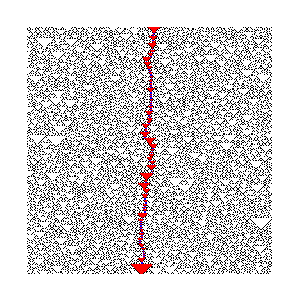

```mathematica
f=aph[HighlightEvenRuns/@CellularAutomaton[146,ParticleInit[300],300]]
```

```mathematica
Export["notebooks/20160105-single-particle.png",f]
```

notebooks/20160105-single-particle.png

```mathematica
f2=aph[CellularAutomaton[146,RandomInteger[1,300],300]]
```

-Graphics-

```mathematica
Export["notebooks/20160105-no-particles.png",f2]
```

notebooks/20160105-no-particles.png